```mathematica
SetDirectory[NotebookDirectory[]];Get["library/FeynCalc.m"]
```

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

SetDirectory::badfile: The specified argument, $Failed, should be a valid string or File object.

TagSetDelayed::write: Tag Commutator in Commutator[a_, b_] = c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_, b_], TraditionalForm] is Protected.

Set::write: Tag Commutator in Commutator[RightPartialD[x_], LeftPartialD[y_]] is Protected.

TagSetDelayed::write: Tag Commutator in Commutator[a_, b_] = c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_, b_], TraditionalForm] is Protected.

```mathematica
FCSetDiracGammaScheme["BMHV"]
```

BMHV

```mathematica
$Assumptions={d>0,e>0,m> 0,v>0,ϵ>0}
```

{d>0,e>0,m>0,v>0,ϵ>0}

## d dimensional momentum integral

```mathematica
Ω[d_]:=(2 π^(d/2))/Gamma[d/2]
```

```mathematica
Ω[d]/(2π)^d Integrate[q^(d-1)q^l(1/((X q^2+Y)^n)),{q,0,∞},Assumptions->{X>0,Y>0,{l,n,d}∈Reals,0≤l≤ 2n}]
```

(2^(-7-d) (-8+d+l) (-6+d+l) (-4+d+l) (-2+d+l) π^(1-d/2) (X/Y)^(1/2 (-d-l)) Csc[1/2 (d+l) π])/(3 Y^5 Gamma[d/2])

```mathematica
ClearAll[Y]
```

```mathematica
ifunc[X_,Y_,d_,n_,l_]:=(2^-d π^(-d/2) (X/Y)^(1/2 (-d-l)) Y^-n Gamma[(d+l)/2] Gamma[-d/2-l/2+n])/(Gamma[d/2] Gamma[n])
```

```mathematica
FVd[d_,q_,i_]:=Pair[LorentzIndex[i,d],Momentum[q,d]]
```

```mathematica
MTd[d_,i_,j_]:=Pair[LorentzIndex[i,d],LorentzIndex[j,d]]
```

```mathematica
wick[d_,indices_,P_]:=Module[{l=Length[indices],intindices,i,ix,f,g,J1,J2,J3},intindices=Table[ix[i],{i,1,l}];f[s_]:=MTd[d,s[[1]],s[[2]]] Signature[s]^P;g[S_]:=Apply[Times,Map[f,Partition[S,2]]];J1=Map[g,Select[Permutations[intindices],Signature[#]==1&]];J2=Map[g,Select[Permutations[intindices],Signature[#]==-1&]];
J3=1/((l/2)!2^(l/2))(Total[J1]+(-1)^P Total[J2])//FullSimplify;J3//.Thread[intindices-> indices]]
```

```mathematica
intcont[d_,q_,indices_]:=Module[{l=Length[indices],norm},norm=1/(Pochhammer[d/2,l/2] 2^(l/2));If[EvenQ[l],norm Pair[Momentum[q,d],Momentum[q,d]]^(l/2)wick[d,indices,0],0]//FullSimplify]
```

```mathematica
LCdC[d_,i_,j_,k_,l_,m_,n_]:=MTd[d,i,l](MTd[d,j,m]MTd[d,k,n]-MTd[d,j,n]MTd[d,k,m])-MTd[d,i,m](MTd[d,j,l]MTd[d,k,n]-MTd[d,j,n]MTd[d,k,l])+MTd[d,i,n](MTd[d,j,l]MTd[d,k,m]-MTd[d,j,m]MTd[d,k,l])
```

```mathematica
SPd[d_,p_,q_]:=Pair[Momentum[p,d],Momentum[q,d]]
```

```mathematica
dband[d_,q_,L_]:=Module[{i,j},√(d/(2(d-1)))Contract[GSD[L[i,j]]FVd[d,q,i]FVd[d,q,j]]]
```

```mathematica
G[d_,w_,q_,L_]:=(-I w+dband[d,q,L]/(2m))/(w^2+SPd[d,q,q]^2/(4 m^2))
```

```mathematica
D0[d_,w_,q_]:=(v^2 SPd[d,q,q])/(w^2+v^2 SPd[d,q,q]^2)
```

```mathematica
D1[d_,w_,q_,i_,j_]:=MTd[d,i,j]/(w^2+v^2 SPd[d,q,q]^2)
```

```mathematica
C0=-I e ;
```

```mathematica
C1[d_,q_,L_,i_]:=Module[{j},-e(√(d/(2(d-1)))Contract[GSD[L[i,j]]FVd[d,q,j]]/(2m))]
```

```mathematica
CubeAniso[d_,q_,arr_,t_,u_,k_,m_]:=-Pair[LorentzIndex[k,d],Momentum[q,d]] Pair[LorentzIndex[m,d],Momentum[q,d]] Pair[LorentzIndex[t,d],LorentzIndex[u,d]] arr[q,{t,u}]+Pair[LorentzIndex[k,d],LorentzIndex[u,d]] Pair[LorentzIndex[m,d],Momentum[q,d]] Pair[LorentzIndex[t,d],Momentum[q,d]] arr[q,{t,u}]+Pair[LorentzIndex[k,d],Momentum[q,d]] Pair[LorentzIndex[m,d],LorentzIndex[t,d]] Pair[LorentzIndex[u,d],Momentum[q,d]] arr[q,{t,u}]-Pair[LorentzIndex[k,d],LorentzIndex[m,d]] Pair[LorentzIndex[t,d],Momentum[q,d]] Pair[LorentzIndex[u,d],Momentum[q,d]] arr[q,{t,u}]-Pair[LorentzIndex[k,d],LorentzIndex[u,d]] Pair[LorentzIndex[m,d],LorentzIndex[t,d]] Pair[Momentum[q,d],Momentum[q,d]] arr[q,{t,u}]+Pair[LorentzIndex[k,d],LorentzIndex[m,d]] Pair[LorentzIndex[t,d],LorentzIndex[u,d]] Pair[Momentum[q,d],Momentum[q,d]] arr[q,{t,u}]
```

```mathematica
LFC[d_,OBX_,L_,LP_,dfunc_,extGammaInd_]:=Module[{A,B,x,i,j,k,l,p,RuleDfunc,RuleDfunc2,Lfunc,finrule},A=OBX//.{Pair[Momentum[L[i_,j_],D],Momentum[L[k_,l_],D]]-> MTd[d,i,k]MTd[d,j,l]+MTd[d,i,l]MTd[d,j,k]-2/d MTd[d,i,j]MTd[d,k,l],Pair[Momentum[L[i_,j_],D],Momentum[LP[k_,l_],D]]-> MTd[d,i,k]MTd[d,j,l]+MTd[d,i,l]MTd[d,j,k]+2/d MTd[d,i,j]MTd[d,k,l],Pair[Momentum[LP[i_,j_],D],Momentum[L[k_,l_],D]]-> MTd[d,i,k]MTd[d,j,l]+MTd[d,i,l]MTd[d,j,k]+2/d MTd[d,i,j]MTd[d,k,l],Pair[Momentum[LP[i_,j_],D],Momentum[LP[k_,l_],D]]-> MTd[d,i,k]MTd[d,j,l]+MTd[d,i,l]MTd[d,j,k]-2/d MTd[d,i,j]MTd[d,k,l]};
B=A//.{Pair[LorentzIndex[i_,d],LorentzIndex[j_,d]]^n_-> Pair[LorentzIndex[i,d],LorentzIndex[j,d]],L[i_,i_]:> 0,L[i_,j_]:> Lfunc[LorentzIndex[i,d],LorentzIndex[j,d]]};;
RuleDfunc[t_]:= Pair[LorentzIndex[t,D],Momentum[Lfunc[Momentum[p_,d],Momentum[p_,d]],D]]:>1/(√(d/(2(d-1))))FVD[dfunc[p],t];
RuleDfunc2[t_]:= Lfunc[LorentzIndex[i_,d],LorentzIndex[i_,d]]:>0;
finrule=Join[Table[RuleDfunc[t],{t,extGammaInd}],Table[RuleDfunc2[t],{t,extGammaInd}]];
FullSimplify[ScalarProductExpand[Contract[B]]//.finrule]]
```

```mathematica
LoopEvaluate[d_,OBX_,w_,q_,arr_,L_,LP_,dfunc_,p0_,p_,ϵ_,extInd_,extGammaInd_]:=Module[{AX,BX,BX1,FreqPoles,FreqPosPoles,ResX,CX,CX1,DX,EX,FX,FX1,CFX,GX,GX1,HX,IX,JX,LX,KX,MX,NX,PX,QX,indexP,denomPW,feynprefact,TabTot,TabS,A,B,PreFactX,X,Y,x,y,z,i,j,k,l,lmax,n,r,s,s1,s2,arrsplit,a1,a2,a3,a4,b1,b2,b3,b4,c1,c2,c3,c4,d1,d2,d3,d4,t,u,t1,t2,t3,t4,Lfunc,NewRule,RuleFunc,NewDRule,RuleDfunc,RuleDfunc2,RuleDfunc3,feynintdom,C1,qFX,qFNORM},
AX=OBX//.{Pair[Momentum[L[i_,j_],D],Momentum[L[k_,l_],D]]-> MTd[d,i,k]MTd[d,j,l]+MTd[d,i,l]MTd[d,j,k]-2/d MTd[d,i,j]MTd[d,k,l],Pair[Momentum[L[i_,j_],D],Momentum[LP[k_,l_],D]]-> MTd[d,i,k]MTd[d,j,l]+MTd[d,i,l]MTd[d,j,k]+2/d MTd[d,i,j]MTd[d,k,l],Pair[Momentum[LP[i_,j_],D],Momentum[L[k_,l_],D]]-> MTd[d,i,k]MTd[d,j,l]+MTd[d,i,l]MTd[d,j,k]+2/d MTd[d,i,j]MTd[d,k,l],Pair[Momentum[LP[i_,j_],D],Momentum[LP[k_,l_],D]]-> MTd[d,i,k]MTd[d,j,l]+MTd[d,i,l]MTd[d,j,k]-2/d MTd[d,i,j]MTd[d,k,l]};
BX=ExpandScalarProduct[ Contract[AX//.{Pair[LorentzIndex[i_,d],LorentzIndex[j_,d]]^n_-> Pair[LorentzIndex[i,d],LorentzIndex[j,d]]}]];(*
BX1=ExpandScalarProduct[FullSimplify[BX/.{w-> z}]];
ResX[x_]:=Residue[BX1,{z,x}];
FreqPoles=z/.Solve[Denominator[BX1]==0,z];
FreqPosPoles=Assuming[Pair[Momentum[p,d],Momentum[q,d]]∈Reals&&p0∈Reals&&Pair[Momentum[p,d],Momentum[p,d]]>0&&Pair[Momentum[q,d],Momentum[q,d]]> 0&&Pair[Momentum[p,d],Momentum[p,d]]+2 Pair[Momentum[p,d],Momentum[q,d]]+Pair[Momentum[q,d],Momentum[q,d]]> 0&&Pair[Momentum[p,d],Momentum[p,d]]-2 Pair[Momentum[p,d],Momentum[q,d]]+Pair[Momentum[q,d],Momentum[q,d]]> 0,Refine[FreqPoles Map[HeavisideTheta,Im[FreqPoles]]]];
CX=FullSimplify[Total[I Map[ResX,FreqPosPoles]],Assumptions-> {Pair[Momentum[p,d],Momentum[q,d]]∈Reals,p0∈Reals,Pair[Momentum[p,d],Momentum[p,d]]>0,Pair[Momentum[q,d],Momentum[q,d]]> 0,Pair[Momentum[p,d],Momentum[p,d]]+2 Pair[Momentum[p,d],Momentum[q,d]]+Pair[Momentum[q,d],Momentum[q,d]]> 0,Pair[Momentum[p,d],Momentum[p,d]]-2 Pair[Momentum[p,d],Momentum[q,d]]+Pair[Momentum[q,d],Momentum[q,d]]> 0}];*)
CX=FullSimplify[Combine[BX]];
DX=FullSimplify[Denominator[Combine[CX]]];
EX=FactorList[DX,Extension->{√2,I}];
n=Length[EX[[All,1]]];
FX=EX/.{Pair[Momentum[q,d],Momentum[q,d]]-> 0,Pair[Momentum[q,d],Momentum[p,d]]-> 0,Pair[Momentum[p,d],Momentum[q,d]]-> 0,Pair[Momentum[p,d],Momentum[p,d]]-> 0,p0-> 0};
C1=Product[If[TrueQ[FX[[i,1]]== 0],1,Evaluate[FX[[i,1]]]],{i,1,n}];
Do[If[TrueQ[FX[[i,1]]== 0],FX[[i,2]]=0],{i,1,n}];
FX1=DeleteCases[(EX-FX),{0,0}];
indexP=FX1[[All,2]];
CFX=Collect[FX1[[All,1]],Pair[Momentum[q,d],Momentum[q,d]]];
r=Length[CFX];
Do[If[TrueQ[Exponent[CFX[[i]],Pair[Momentum[q,d],Momentum[q,d]]]>2],Print["The computations failed because no feynman parametrization could be performed!"]],{i,1,r}];
qFX=CFX/.{t_ Pair[Momentum[q,d],Momentum[q,d]]+u_-> Pair[Momentum[q,d],Momentum[q,d]]+u/t,t_ Pair[Momentum[q,d],Momentum[q,d]]-> Pair[Momentum[q,d],Momentum[q,d]]};
qFNORM=Apply[Times,CFX/.{t_ Pair[Momentum[q,d],Momentum[q,d]]+u_-> t,t_ Pair[Momentum[q,d],Momentum[q,d]]-> t,Pair[Momentum[q,d],Momentum[q,d]]+u_-> 1,Pair[Momentum[q,d],Momentum[q,d]]-> 1}];
denomPW=Total[indexP];
feynprefact=Gamma[denomPW]/Apply[Times,Map[Gamma,indexP]];
TabS=Table[x[i],{i,1,r}];
TabTot=Total[TabS];
feynintdom=Table[{x[i],0,1},{i,1,r}];
GX=Collect2[Total[Table[TabS[[i]]qFX[[i]],{i,1,r}]],Pair[Momentum[q,d],Momentum[q,d]],Factoring-> FullSimplify]/.{TabTot-> 1};
HX=Product[TabS[[i]]^(indexP[[i]]-1),{i,1,r}];
PreFactX=feynprefact/(C1 qFNORM) HX ;
A=Coefficient[GX,Pair[Momentum[q,d],Momentum[q,d]]];
B=Coefficient[GX,Pair[Momentum[p,d],Momentum[q,d]]];
IX=Simplify[ExpandScalarProduct[PreFactX Numerator[CX]/.{Momentum[q,d]-> (Momentum[q,d]-B/(2A)Momentum[p,d])}]];
RuleFunc[t_]:=Pair[LorentzIndex[t,d],Momentum[p,d]]:> arr[p,{t}];
NewRule=Join[{Pair[LorentzIndex[t_,d],Momentum[q,d]]:> arr[q,{t}],Pair[Momentum[p,d],Momentum[q,d]]:> arr[p,{a1}]arr[q,{a1}],Pair[Momentum[p,d],Momentum[q,d]]^2:> arr[p,{a2,b2}]arr[q,{a2,b2}],Pair[Momentum[p,d],Momentum[q,d]]^3:> arr[p,{a3,b3,c3}]arr[q,{a3,b3,c3}],Pair[Momentum[p,d],Momentum[q,d]]^4:> arr[p,{a4,b4,c4,d4}]arr[q,{a4,b4,c4,d4}]},Table[RuleFunc[t],{t,extInd}]];
JX=ExpandAll2[IX]//.NewRule;
arrsplit[x_,s_]:=Apply[Times,Table[FVd[d,x,i],{i,s}]];
KX=JX//.{arr[q,s1_]arr[q,s2_]-> arr[q,Join[s1,s2]],arr[q,s_]^2-> arr[q,Join[s,s]],arr[q,s_]^4-> arr[q,Join[s,s,s,s]],arr[p,s1_]arr[p,s2_]-> arr[p,Join[s1,s2]],arr[p,s_]^2-> arr[p,Join[s,s]],arr[p,s_]^4-> arr[p,Join[s,s,s,s]]};
LX=KX//.{arr[q,s_]:> intcont[d,q,s]};
MX=LX//.{Pair[LorentzIndex[i_,d],LorentzIndex[j_,d]]^n_-> Pair[LorentzIndex[i,d],LorentzIndex[j,d]],L[i_,i_]:> 0,L[i_,j_]:> Lfunc[LorentzIndex[i,d],LorentzIndex[j,d]],arr[p,s_]:> arrsplit[p,s]};
RuleDfunc[t_]:= Pair[LorentzIndex[t,D],Momentum[Lfunc[Momentum[p,d],Momentum[p,d]],D]]:>1/(√(d/(2(d-1))))FVD[dfunc[p],t];
RuleDfunc2[t_]:= Lfunc[LorentzIndex[i_,d],LorentzIndex[i_,d]]:>0;
NewDRule=Join[Table[RuleDfunc[t],{t,extGammaInd}],Table[RuleDfunc2[t],{t,extGammaInd}]];
NX=Contract[MX]//.NewDRule//ExpandAll2;
GX1=FullSimplify[ExpandScalarProduct[GX/.{Momentum[q,d]-> Momentum[q,d]-B/(2A)Momentum[p,d]}]];
X=Coefficient[GX1,Pair[Momentum[q,d],Momentum[q,d]],1];
Y=Coefficient[GX1,Pair[Momentum[q,d],Momentum[q,d]],0];
lmax=Exponent[NX,Pair[Momentum[q,d],Momentum[q,d]]];
PX=Sum[Coefficient[NX,Pair[Momentum[q,d],Momentum[q,d]],l]ifunc[X,Y,d,denomPW,2l],{l,0,lmax}]/.{Pair[LorentzIndex[i_,d],Momentum[p,d]]-> p[i],Pair[LorentzIndex[i_,d],LorentzIndex[j_,d]]-> KroneckerDelta[i,j],Pair[Momentum[p,d],Momentum[p,d]]-> p^2};
QX=SeriesCoefficient[PX/.{d-> 4-ϵ},{ϵ,0,-1}] 1/ϵ;
Print[QX//TraditionalForm];
Integrate[QX DiracDelta[1-TabTot],Evaluate[Sequence@@feynintdom]]]
```

## Computation in the symmetric limit

## Computation for δZ_1

```mathematica
L1=C1[q,L,i].G[k0+q0,q,L].C1[q,L,j]D1[q0,q,i,j];
L2=C0 G[k0+q0,q,L]C0 D0[q0,q];
LoopInt=TR[L1+L2,Contract-> False];
CT=TR[-Subscript[δZ, 1](I k0),Contract-> False];
LEQ1=LoopEvaluate[LoopInt,q0,q,qarr,L,LP,d,k0,k,ϵ,{},{}]+LFC[CT,L,LP,d,{}];
LEQ1//TraditionalForm
```

LoopEvaluate(4 (C1(q,L,i) C1(q,L,j) D1(q0,q,i,j) G(k0+q0,q,L)-e^2 D0(q0,q) G(k0+q0,q,L)),q0,q,qarr,L,LP,d,k0,k,ϵ,{},{})+LFC(-4 ⅈ δZ_1 k0,L,LP,d,{})

```mathematica
SOL1=Collect2[Solve[LEQ1==0,Subscript[δZ, 1]],ϵ,Factoring-> FullSimplify];
SOL1//TraditionalForm
```

{{δZ_1→1/(4 k0)ⅈ InverseFunction[LFC,1,5][-LoopEvaluate(4 (C1(q,L,i) C1(q,L,j) D1(q0,q,i,j) G(k0+q0,q,L)-e^2 D0(q0,q) G(k0+q0,q,L)),q0,q,qarr,L,LP,d,k0,k,ϵ,{},{}),L,LP,d,{}]}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

## Computation for δZ_2

```mathematica
LoopInt1=C1[q+2k,L,i].G[q0,k+q,L].C1[q+2k,L,j]D1[q0,q,i,j];
LoopInt2=C0 G[q0,k+q,L]C0 D0[q0,q];
CT=-Subscript[δZ, 2] dband[k,L]/(2m);
CTObj=TR[CT.GAD[a],Contract-> False];
TrObj=TR[(LoopInt1+LoopInt2).GAD[a],Contract-> False];
LEQ2=LoopEvaluate[TrObj,q0,q,qarr,L,LP,d,k0,k,ϵ,{},{a}]+LFC[CTObj,L,LP,d,{a}];
LEQ2//TraditionalForm
```

LoopEvaluate(0,q0,q,qarr,L,LP,d,k0,k,ϵ,{},{a})+LFC(0,L,LP,d,{a})

```mathematica
SOL2=Collect2[Solve[LEQ2==0,Subscript[δZ, 2]],ϵ,Factoring-> FullSimplify];
SOL2//TraditionalForm
```

{}

## Computation for δZ_3

```mathematica
LoopInt=TR[-(C0).G[q0,q+k,L].(C0).G[q0,q,L],Contract-> False];
LoopEvaluate[LoopInt,q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}]
```

LoopEvaluate[4 e^2 G[q0,q,L] G[q0,k+q,L],q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}]

```mathematica
LoopInt=TR[-(C0).G[q0,q+k,L].(C0).G[q0,q,L],Contract-> False];
CT=-Subscript[δZ, 3] k^2;
LEQ3=LoopEvaluate[LoopInt,q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}]+LFC[CT,L,LP,d,{}];
LEQ3//TraditionalForm
```

LoopEvaluate(4 e^2 G(q0,q,L) G(q0,k+q,L),q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{})+LFC(δZ_3 (-k^2),L,LP,d,{})

```mathematica
SOL3=Collect2[Solve[LEQ3==0,Subscript[δZ, 3]],ϵ,Factoring-> FullSimplify];
SOL3//TraditionalForm
```

{{δZ_3→-1/k^2 InverseFunction[LFC,1,5][-LoopEvaluate(4 e^2 G(q0,q,L) G(q0,k+q,L),q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}),L,LP,d,{}]}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

## (Spatial) transverse and longitudinal projectors

```mathematica
PT[p_,i_,j_]:=MTd[d,i,j]-(FVd[d,p,i]FVd[d,p,j])/SPd[d,p,p]
```

```mathematica
PL[p_,i_,j_]:=(FVd[d,p,i]FVd[d,p,j])/SPd[d,p,p]
```

```mathematica
2^(d/2)/4 TR[GAD[a].GAD[b]]
```

2^(d/2) Pair[LorentzIndex[a,D],LorentzIndex[b,D]]

```mathematica
2^(d/2)/4 TR[GAD[a].GAD[b].GAD[c].GAD[d]]//TraditionalForm
```

2^(d/2) (g^ad g^bc-g^ac g^bd+g^ab g^cd)

## Computation for δZ_4

#### Transverse part of the renormalized vacuum polarization

```mathematica
LoopInt=TR[-C1[d,k+2q,L,i].G[d,0,k+q,L].C1[d,k+2q,L,j].G[d,0,q,L],Contract-> False];
LEX=LoopEvaluate[d,LoopInt,q0,q,arr,L,LP,d,k0,k,ϵ,{i,j},{}]
```

(e^2 (175 k[i] k[j]-158 k^2 i,j))/(30 π^2 ϵ)

```mathematica
FullSimplify[LEX//N]//TraditionalForm
```

(e^2 (0.59104 k(i) k(j)-0.533625 k^2 i,j))/ϵ

```mathematica
LoopInt=TR[-C1[d,k+2q,L,i].G[d,q0,k+q,L].C1[d,k+2q,L,l].G[d,q0,q,L],Contract-> False];
CT=-Subscript[δZ, 4] v^2 SPd[d,k,k]^2 PT[k,i,l] ;
LE4=LoopEvaluate[d,dc,LoopInt,q0,q,qarr,L,LP,d,k0,k,ϵ,{i,l},{}]+CT;
LEQ4=LFC[d,Contract[(LE4)PT[k,l,j]],L,LP,d,{}];
Collect[Collect2[LEQ4,PT[k,i,j],Factoring-> FullSimplify],{PT[k,i,j],q,Subscript[δZ, 4],v},FullSimplify]
```

LoopEvaluate[d,dc,(2 e^2 (d Pair[LorentzIndex[i,d],LorentzIndex[j,d]] (Pair[Momentum[k,d],Momentum[k,d]]+4 (Pair[Momentum[k,d],Momentum[q,d]]+Pair[Momentum[q,d],Momentum[q,d]])) (-d Pair[Momentum[k,d],Momentum[q,d]]^2+Pair[Momentum[k,d],Momentum[k,d]] Pair[Momentum[q,d],Momentum[q,d]]-2 (-1+d) Pair[Momentum[k,d],Momentum[q,d]] Pair[Momentum[q,d],Momentum[q,d]]-(-1+d) (4 m^2 q0^2+Pair[Momentum[q,d],Momentum[q,d]]^2))+Pair[LorentzIndex[i,d],Momentum[k,d]] (Pair[LorentzIndex[j,d],Momentum[k,d]] ((-2+d) (-4 (-1+d) m^2 q0^2-d Pair[Momentum[k,d],Momentum[q,d]]^2)+((2-3 d) Pair[Momentum[k,d],Momentum[k,d]]-2 (-2+d (3+d)) Pair[Momentum[k,d],Momentum[q,d]]) Pair[Momentum[q,d],Momentum[q,d]]-(-2+d (5+d)) Pair[Momentum[q,d],Momentum[q,d]]^2)+2 Pair[LorentzIndex[j,d],Momentum[q,d]] (2 d^2 Pair[Momentum[k,d],Momentum[q,d]]^2+2 (2+d (-4+3 d)) Pair[Momentum[k,d],Momentum[q,d]] Pair[Momentum[q,d],Momentum[q,d]]+(-1+d) Pair[Momentum[k,d],Momentum[k,d]] (d Pair[Momentum[k,d],Momentum[q,d]]+2 (-1+d) Pair[Momentum[q,d],Momentum[q,d]])+(-1+d) (-4 (-2+d) m^2 q0^2+(-2+3 d) Pair[Momentum[q,d],Momentum[q,d]]^2)))+2 Pair[LorentzIndex[i,d],Momentum[q,d]] (Pair[LorentzIndex[j,d],Momentum[k,d]] (2 d^2 Pair[Momentum[k,d],Momentum[q,d]]^2+2 (2+d (-4+3 d)) Pair[Momentum[k,d],Momentum[q,d]] Pair[Momentum[q,d],Momentum[q,d]]+(-1+d) Pair[Momentum[k,d],Momentum[k,d]] (d Pair[Momentum[k,d],Momentum[q,d]]+2 (-1+d) Pair[Momentum[q,d],Momentum[q,d]])+(-1+d) (-4 (-2+d) m^2 q0^2+(-2+3 d) Pair[Momentum[q,d],Momentum[q,d]]^2))+2 Pair[LorentzIndex[j,d],Momentum[q,d]] ((-2+d) Pair[Momentum[k,d],Momentum[k,d]] (d Pair[Momentum[k,d],Momentum[q,d]]+(-1+2 d) Pair[Momentum[q,d],Momentum[q,d]])+(-1+d) (-4 (-2+d) m^2 q0^2+2 d Pair[Momentum[k,d],Momentum[q,d]]^2+2 (-2+3 d) Pair[Momentum[k,d],Momentum[q,d]] Pair[Momentum[q,d],Momentum[q,d]]+(-2+3 d) Pair[Momentum[q,d],Momentum[q,d]]^2)))))/((1-d) (-1+d) (4 m^2 q0^2+Pair[Momentum[q,d],Momentum[q,d]]^2) (4 m^2 q0^2+(Pair[Momentum[k,d],Momentum[k,d]]+2 Pair[Momentum[k,d],Momentum[q,d]]+Pair[Momentum[q,d],Momentum[q,d]])^2)),q0,q,qarr,L,LP,d,k0,k,ϵ,{i,l},{}]-(LoopEvaluate[d,dc,(2 e^2 (d Pair[LorentzIndex[i,d],LorentzIndex[l,d]] (Pair[Momentum[k,d],Momentum[k,d]]+4 (Pair[Momentum[k,d],Momentum[q,d]]+Pair[Momentum[q,d],Momentum[q,d]])) (-d Pair[Momentum[k,d],Momentum[q,d]]^2+Pair[Momentum[k,d],Momentum[k,d]] Pair[Momentum[q,d],Momentum[q,d]]-2 (-1+d) Pair[Momentum[k,d],Momentum[q,d]] Pair[Momentum[q,d],Momentum[q,d]]-(-1+d) (4 m^2 q0^2+Pair[Momentum[q,d],Momentum[q,d]]^2))+Pair[LorentzIndex[i,d],Momentum[k,d]] (Pair[LorentzIndex[l,d],Momentum[k,d]] ((-2+d) (-4 (-1+d) m^2 q0^2-d Pair[Momentum[k,d],Momentum[q,d]]^2)+((2-3 d) Pair[Momentum[k,d],Momentum[k,d]]-2 (-2+d (3+d)) Pair[Momentum[k,d],Momentum[q,d]]) Pair[Momentum[q,d],Momentum[q,d]]-(-2+d (5+d)) Pair[Momentum[q,d],Momentum[q,d]]^2)+2 Pair[LorentzIndex[l,d],Momentum[q,d]] (2 d^2 Pair[Momentum[k,d],Momentum[q,d]]^2+2 (2+d (-4+3 d)) Pair[Momentum[k,d],Momentum[q,d]] Pair[Momentum[q,d],Momentum[q,d]]+(-1+d) Pair[Momentum[k,d],Momentum[k,d]] (d Pair[Momentum[k,d],Momentum[q,d]]+2 (-1+d) Pair[Momentum[q,d],Momentum[q,d]])+(-1+d) (-4 (-2+d) m^2 q0^2+(-2+3 d) Pair[Momentum[q,d],Momentum[q,d]]^2)))+2 Pair[LorentzIndex[i,d],Momentum[q,d]] (Pair[LorentzIndex[l,d],Momentum[k,d]] (2 d^2 Pair[Momentum[k,d],Momentum[q,d]]^2+2 (2+d (-4+3 d)) Pair[Momentum[k,d],Momentum[q,d]] Pair[Momentum[q,d],Momentum[q,d]]+(-1+d) Pair[Momentum[k,d],Momentum[k,d]] (d Pair[Momentum[k,d],Momentum[q,d]]+2 (-1+d) Pair[Momentum[q,d],Momentum[q,d]])+(-1+d) (-4 (-2+d) m^2 q0^2+(-2+3 d) Pair[Momentum[q,d],Momentum[q,d]]^2))+2 Pair[LorentzIndex[l,d],Momentum[q,d]] ((-2+d) Pair[Momentum[k,d],Momentum[k,d]] (d Pair[Momentum[k,d],Momentum[q,d]]+(-1+2 d) Pair[Momentum[q,d],Momentum[q,d]])+(-1+d) (-4 (-2+d) m^2 q0^2+2 d Pair[Momentum[k,d],Momentum[q,d]]^2+2 (-2+3 d) Pair[Momentum[k,d],Momentum[q,d]] Pair[Momentum[q,d],Momentum[q,d]]+(-2+3 d) Pair[Momentum[q,d],Momentum[q,d]]^2)))))/((1-d) (-1+d) (4 m^2 q0^2+Pair[Momentum[q,d],Momentum[q,d]]^2) (4 m^2 q0^2+(Pair[Momentum[k,d],Momentum[k,d]]+2 Pair[Momentum[k,d],Momentum[q,d]]+Pair[Momentum[q,d],Momentum[q,d]])^2)),q0,q,qarr,L,LP,d,k0,k,ϵ,{i,l},{}] Pair[LorentzIndex[j,d],Momentum[k,d]])/Pair[Momentum[k,d],Momentum[k,d]]+v^2 Pair[Momentum[k,d],Momentum[k,d]] (Pair[LorentzIndex[i,d],Momentum[k,d]] Pair[LorentzIndex[j,d],Momentum[k,d]]-Pair[LorentzIndex[i,d],LorentzIndex[j,d]] Pair[Momentum[k,d],Momentum[k,d]]) δZ_4

#### Longitudinal part of the renormalized vacuum polarization

```mathematica
LEQ4p=LFC[d,Contract[(LE4)PL[k,l,j]],L,LP,d,{}];
Collect[Collect2[LEQ4p,PL[k,i,j],Factoring-> FullSimplify],{PL[k,i,j],q,Subscript[δZ, 4],v},FullSimplify]//TraditionalForm
```

1/k^2 k^j LoopEvaluate(d,dc,(2 e^2 (k^i (2 q^l (2 d^2 (k·q)^2+2 (d (3 d-4)+2) q^2 (k·q)+(d-1) k^2 (d (k·q)+2 (d-1) q^2)+(d-1) ((3 d-2) q^4-4 (d-2) m^2 q0^2))+k^l ((d-2) (-d (k·q)^2-4 (d-1) m^2 q0^2)+q^2 ((2-3 d) k^2-2 (d (d+3)-2) (k·q))-((d (d+5)-2) q^4)))+2 q^i (k^l (2 d^2 (k·q)^2+2 (d (3 d-4)+2) q^2 (k·q)+(d-1) k^2 (d (k·q)+2 (d-1) q^2)+(d-1) ((3 d-2) q^4-4 (d-2) m^2 q0^2))+2 q^l ((d-1) (2 d (k·q)^2+2 (3 d-2) q^2 (k·q)-4 (d-2) m^2 q0^2+(3 d-2) q^4)+(d-2) k^2 (d (k·q)+(2 d-1) q^2)))+d g^il (4 (k·q+q^2)+k^2) (-d (k·q)^2-2 (d-1) q^2 (k·q)-(d-1) (4 m^2 q0^2+q^4)+k^2 q^2)))/((1-d) (d-1) (4 m^2 q0^2+q^4) ((2 (k·q)+k^2+q^2)^2+4 m^2 q0^2)),q0,q,qarr,L,LP,d,k0,k,ϵ,{i,l},{})

```mathematica
Solve[d (7 d-83)+31==0,d]
```

{{d→1/14 (83-3 √669)},{d→1/14 (83+3 √669)}}

```mathematica
SOL4=Collect2[Solve[LEQ4==0,Subscript[δZ, 4]],q,Factoring-> FullSimplify];
SOL4//TraditionalForm
```

{{δZ_4→1/(v^2 k^2 (g^ij k^2-k^i k^j))LoopEvaluate(d,dc,(2 e^2 (d g^ij (k^2+4 (k·q+q^2)) (-d (k·q)^2-2 (d-1) q^2 (k·q)+k^2 q^2-(d-1) (4 m^2 q0^2+q^4))+k^i (k^j (-((d (d+5)-2) q^4)+((2-3 d) k^2-2 (d (d+3)-2) (k·q)) q^2+(d-2) (-4 (d-1) m^2 q0^2-d (k·q)^2))+2 q^j (2 d^2 (k·q)^2+2 (d (3 d-4)+2) q^2 (k·q)+(d-1) k^2 (d (k·q)+2 (d-1) q^2)+(d-1) ((3 d-2) q^4-4 (d-2) m^2 q0^2)))+2 q^i (k^j (2 d^2 (k·q)^2+2 (d (3 d-4)+2) q^2 (k·q)+(d-1) k^2 (d (k·q)+2 (d-1) q^2)+(d-1) ((3 d-2) q^4-4 (d-2) m^2 q0^2))+2 q^j ((d-2) k^2 (d (k·q)+(2 d-1) q^2)+(d-1) (-4 (d-2) m^2 q0^2+2 d (k·q)^2+(3 d-2) q^4+2 (3 d-2) (k·q) q^2)))))/((1-d) (d-1) (4 m^2 q0^2+q^4) (4 m^2 q0^2+(k^2+2 (k·q)+q^2)^2)),q0,q,qarr,L,LP,d,k0,k,ϵ,{i,l},{})+1/(v^2 k^4 (k^i k^j-g^ij k^2))LoopEvaluate(d,dc,(2 e^2 (d g^il (k^2+4 (k·q+q^2)) (-d (k·q)^2-2 (d-1) q^2 (k·q)+k^2 q^2-(d-1) (4 m^2 q0^2+q^4))+k^i (k^l (-((d (d+5)-2) q^4)+((2-3 d) k^2-2 (d (d+3)-2) (k·q)) q^2+(d-2) (-4 (d-1) m^2 q0^2-d (k·q)^2))+2 q^l (2 d^2 (k·q)^2+2 (d (3 d-4)+2) q^2 (k·q)+(d-1) k^2 (d (k·q)+2 (d-1) q^2)+(d-1) ((3 d-2) q^4-4 (d-2) m^2 q0^2)))+2 q^i (k^l (2 d^2 (k·q)^2+2 (d (3 d-4)+2) q^2 (k·q)+(d-1) k^2 (d (k·q)+2 (d-1) q^2)+(d-1) ((3 d-2) q^4-4 (d-2) m^2 q0^2))+2 q^l ((d-2) k^2 (d (k·q)+(2 d-1) q^2)+(d-1) (-4 (d-2) m^2 q0^2+2 d (k·q)^2+(3 d-2) q^4+2 (3 d-2) (k·q) q^2)))))/((1-d) (d-1) (4 m^2 q0^2+q^4) (4 m^2 q0^2+(k^2+2 (k·q)+q^2)^2)),q0,q,qarr,L,LP,d,k0,k,ϵ,{i,l},{}) k^j}}

## Computation of the gamma and beta functions

```mathematica
dZarr={1+Subscript[δZ, 1],1+Subscript[δZ, 2],1+ Subscript[δZ, 3],1+ Subscript[δZ, 4]}/.Flatten[Join[SOL1,SOL2,SOL3,SOL4]];
{Z1,Z2,Z3,Z4}=FullSimplify[FullSimplify[dZarr//.{e^2-> g1/m,m-> 1/(g2 √v)}]]
```

{1+1/(4 k0)ⅈ InverseFunction[LFC,1,5][-LoopEvaluate[4 (-g1 g2 √v D0[q0,q]+C1[q,L,i] C1[q,L,j] D1[q0,q,i,j]) G[k0+q0,q,L],q0,q,qarr,L,LP,d,k0,k,ϵ,{},{}],L,LP,d,{}],1+δZ_2,1-1/k^2 InverseFunction[LFC,1,5][-LoopEvaluate[4 g1 g2 √v G[q0,q,L] G[q0,k+q,L],q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}],L,LP,d,{}],1+(-LoopEvaluate[d,dc,(2 g1 g2 √v (d Pair[LorentzIndex[i,d],LorentzIndex[l,d]] (Pair[Momentum[k,d],Momentum[k,d]]+4 (Pair[Momentum[k,d],Momentum[q,d]]+Pair[Momentum[q,d],Momentum[q,d]])) (-d Pair[Momentum[k,d],Momentum[q,d]]^2+Pair[Momentum[k,d],Momentum[k,d]] Pair[Momentum[q,d],Momentum[q,d]]-2 (-1+d) Pair[Momentum[k,d],Momentum[q,d]] Pair[Momentum[q,d],Momentum[q,d]]-(-1+d) ((4 q0^2)/(g2^2 v)+Pair[Momentum[q,d],Momentum[q,d]]^2))+Pair[LorentzIndex[i,d],Momentum[k,d]] (Pair[LorentzIndex[l,d],Momentum[k,d]] ((-2+d) (-(4 (-1+d) q0^2)/(g2^2 v)-d Pair[Momentum[k,d],Momentum[q,d]]^2)+((2-3 d) Pair[Momentum[k,d],Momentum[k,d]]-2 (-2+d (3+d)) Pair[Momentum[k,d],Momentum[q,d]]) Pair[Momentum[q,d],Momentum[q,d]]-(-2+d (5+d)) Pair[Momentum[q,d],Momentum[q,d]]^2)+2 Pair[LorentzIndex[l,d],Momentum[q,d]] (2 d^2 Pair[Momentum[k,d],Momentum[q,d]]^2+2 (2+d (-4+3 d)) Pair[Momentum[k,d],Momentum[q,d]] Pair[Momentum[q,d],Momentum[q,d]]+(-1+d) Pair[Momentum[k,d],Momentum[k,d]] (d Pair[Momentum[k,d],Momentum[q,d]]+2 (-1+d) Pair[Momentum[q,d],Momentum[q,d]])+(-1+d) (-(4 (-2+d) q0^2)/(g2^2 v)+(-2+3 d) Pair[Momentum[q,d],Momentum[q,d]]^2)))+2 Pair[LorentzIndex[i,d],Momentum[q,d]] (Pair[LorentzIndex[l,d],Momentum[k,d]] (2 d^2 Pair[Momentum[k,d],Momentum[q,d]]^2+2 (2+d (-4+3 d)) Pair[Momentum[k,d],Momentum[q,d]] Pair[Momentum[q,d],Momentum[q,d]]+(-1+d) Pair[Momentum[k,d],Momentum[k,d]] (d Pair[Momentum[k,d],Momentum[q,d]]+2 (-1+d) Pair[Momentum[q,d],Momentum[q,d]])+(-1+d) (-(4 (-2+d) q0^2)/(g2^2 v)+(-2+3 d) Pair[Momentum[q,d],Momentum[q,d]]^2))+2 Pair[LorentzIndex[l,d],Momentum[q,d]] ((-2+d) Pair[Momentum[k,d],Momentum[k,d]] (d Pair[Momentum[k,d],Momentum[q,d]]+(-1+2 d) Pair[Momentum[q,d],Momentum[q,d]])+(-1+d) (-(4 (-2+d) q0^2)/(g2^2 v)+2 d Pair[Momentum[k,d],Momentum[q,d]]^2+2 (-2+3 d) Pair[Momentum[k,d],Momentum[q,d]] Pair[Momentum[q,d],Momentum[q,d]]+(-2+3 d) Pair[Momentum[q,d],Momentum[q,d]]^2)))))/((1-d) (-1+d) ((4 q0^2)/(g2^2 v)+Pair[Momentum[q,d],Momentum[q,d]]^2) ((4 q0^2)/(g2^2 v)+(Pair[Momentum[k,d],Momentum[k,d]]+2 Pair[Momentum[k,d],Momentum[q,d]]+Pair[Momentum[q,d],Momentum[q,d]])^2)),q0,q,qarr,L,LP,d,k0,k,ϵ,{i,l},{}] Pair[LorentzIndex[j,d],Momentum[k,d]]+LoopEvaluate[d,dc,(2 g1 g2 √v (d Pair[LorentzIndex[i,d],LorentzIndex[j,d]] (Pair[Momentum[k,d],Momentum[k,d]]+4 (Pair[Momentum[k,d],Momentum[q,d]]+Pair[Momentum[q,d],Momentum[q,d]])) (-d Pair[Momentum[k,d],Momentum[q,d]]^2+Pair[Momentum[k,d],Momentum[k,d]] Pair[Momentum[q,d],Momentum[q,d]]-2 (-1+d) Pair[Momentum[k,d],Momentum[q,d]] Pair[Momentum[q,d],Momentum[q,d]]-(-1+d) ((4 q0^2)/(g2^2 v)+Pair[Momentum[q,d],Momentum[q,d]]^2))+Pair[LorentzIndex[i,d],Momentum[k,d]] (Pair[LorentzIndex[j,d],Momentum[k,d]] ((-2+d) (-(4 (-1+d) q0^2)/(g2^2 v)-d Pair[Momentum[k,d],Momentum[q,d]]^2)+((2-3 d) Pair[Momentum[k,d],Momentum[k,d]]-2 (-2+d (3+d)) Pair[Momentum[k,d],Momentum[q,d]]) Pair[Momentum[q,d],Momentum[q,d]]-(-2+d (5+d)) Pair[Momentum[q,d],Momentum[q,d]]^2)+2 Pair[LorentzIndex[j,d],Momentum[q,d]] (2 d^2 Pair[Momentum[k,d],Momentum[q,d]]^2+2 (2+d (-4+3 d)) Pair[Momentum[k,d],Momentum[q,d]] Pair[Momentum[q,d],Momentum[q,d]]+(-1+d) Pair[Momentum[k,d],Momentum[k,d]] (d Pair[Momentum[k,d],Momentum[q,d]]+2 (-1+d) Pair[Momentum[q,d],Momentum[q,d]])+(-1+d) (-(4 (-2+d) q0^2)/(g2^2 v)+(-2+3 d) Pair[Momentum[q,d],Momentum[q,d]]^2)))+2 Pair[LorentzIndex[i,d],Momentum[q,d]] (Pair[LorentzIndex[j,d],Momentum[k,d]] (2 d^2 Pair[Momentum[k,d],Momentum[q,d]]^2+2 (2+d (-4+3 d)) Pair[Momentum[k,d],Momentum[q,d]] Pair[Momentum[q,d],Momentum[q,d]]+(-1+d) Pair[Momentum[k,d],Momentum[k,d]] (d Pair[Momentum[k,d],Momentum[q,d]]+2 (-1+d) Pair[Momentum[q,d],Momentum[q,d]])+(-1+d) (-(4 (-2+d) q0^2)/(g2^2 v)+(-2+3 d) Pair[Momentum[q,d],Momentum[q,d]]^2))+2 Pair[LorentzIndex[j,d],Momentum[q,d]] ((-2+d) Pair[Momentum[k,d],Momentum[k,d]] (d Pair[Momentum[k,d],Momentum[q,d]]+(-1+2 d) Pair[Momentum[q,d],Momentum[q,d]])+(-1+d) (-(4 (-2+d) q0^2)/(g2^2 v)+2 d Pair[Momentum[k,d],Momentum[q,d]]^2+2 (-2+3 d) Pair[Momentum[k,d],Momentum[q,d]] Pair[Momentum[q,d],Momentum[q,d]]+(-2+3 d) Pair[Momentum[q,d],Momentum[q,d]]^2)))))/((1-d) (-1+d) ((4 q0^2)/(g2^2 v)+Pair[Momentum[q,d],Momentum[q,d]]^2) ((4 q0^2)/(g2^2 v)+(Pair[Momentum[k,d],Momentum[k,d]]+2 Pair[Momentum[k,d],Momentum[q,d]]+Pair[Momentum[q,d],Momentum[q,d]])^2)),q0,q,qarr,L,LP,d,k0,k,ϵ,{i,l},{}] Pair[Momentum[k,d],Momentum[k,d]])/(v^2 Pair[Momentum[k,d],Momentum[k,d]]^2 (-Pair[LorentzIndex[i,d],Momentum[k,d]] Pair[LorentzIndex[j,d],Momentum[k,d]]+Pair[LorentzIndex[i,d],LorentzIndex[j,d]] Pair[Momentum[k,d],Momentum[k,d]]))}

```mathematica
γ1[β1_,β2_]:=β1 D[Log[Z1],g1]+β2 D[Log[Z1],g2];
γ2[β1_,β2_]:=β1 D[Log[Z2],g1]+β2 D[Log[Z2],g2];
γ3[β1_,β2_]:=β1 D[Log[Z3],g1]+β2 D[Log[Z3],g2];
γ4[β1_,β2_]:=β1 D[Log[Z4],g1]+β2 D[Log[Z4],g2];
```

```mathematica
BetaFunc={β1,β2}/.Flatten[Solve[β1==-(ϵ+γ1[β1,β2]-(γ2[β1,β2]+γ3[β1,β2]))g1&&β2==(γ1[β1,β2]-γ2[β1,β2]-1/2(γ3[β1,β2]-γ4[β1,β2]))g2,{β1,β2}]];
```

```mathematica
Collect[Series[BetaFunc,{g1,0,2}]/.{1/ϵ-> 0}//Normal,ϵ,FullSimplify]
```

{g1 ϵ (-1+4 g1 g2 √v ((ⅈ D0[q0,q] G[k0+q0,q,L] InverseFunction[LFC,1,5]^(1,0,0,0)[-LoopEvaluate[4 C1[q,L,i] C1[q,L,j] D1[q0,q,i,j] G[k0+q0,q,L],q0,q,qarr,L,LP,d,k0,k,ϵ,{},{}],L,LP,d,{}] LoopEvaluate^(1,0,0,0,0,0,0,0,0,0)[4 C1[q,L,i] C1[q,L,j] D1[q0,q,i,j] G[k0+q0,q,L],q0,q,qarr,L,LP,d,k0,k,ϵ,{},{}])/(4 k0+ⅈ InverseFunction[LFC,1,5][-LoopEvaluate[4 C1[q,L,i] C1[q,L,j] D1[q0,q,i,j] G[k0+q0,q,L],q0,q,qarr,L,LP,d,k0,k,ϵ,{},{}],L,LP,d,{}])+(G[q0,q,L] G[q0,k+q,L] InverseFunction[LFC,1,5]^(1,0,0,0)[-LoopEvaluate[0,q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}],L,LP,d,{}] LoopEvaluate^(1,0,0,0,0,0,0,0,0,0,{0})[0,q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}])/(-k^2+InverseFunction[LFC,1,5][-LoopEvaluate[0,q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}],L,LP,d,{}]))),2 g1 g2^2 √v ϵ ((8 g1 g2 √v D0[q0,q]^2 G[k0+q0,q,L]^2 (-(((InverseFunction[LFC,1,5]^(1,0,0,0)[-LoopEvaluate[4 C1[q,L,i] C1[q,L,j] D1[q0,q,i,j] G[k0+q0,q,L],q0,q,qarr,L,LP,d,k0,k,ϵ,{},{}],L,LP,d,{}])^2+(4 ⅈ k0-InverseFunction[LFC,1,5][-LoopEvaluate[4 C1[q,L,i] C1[q,L,j] D1[q0,q,i,j] G[k0+q0,q,L],q0,q,qarr,L,LP,d,k0,k,ϵ,{},{}],L,LP,d,{}]) InverseFunction[LFC,1,5]^(2,0,0,0)[-LoopEvaluate[4 C1[q,L,i] C1[q,L,j] D1[q0,q,i,j] G[k0+q0,q,L],q0,q,qarr,L,LP,d,k0,k,ϵ,{},{}],L,LP,d,{}]) (LoopEvaluate^(1,0,0,0,0,0,0,0,0,0)[4 C1[q,L,i] C1[q,L,j] D1[q0,q,i,j] G[k0+q0,q,L],q0,q,qarr,L,LP,d,k0,k,ϵ,{},{}])^2)+(4 ⅈ k0-InverseFunction[LFC,1,5][-LoopEvaluate[4 C1[q,L,i] C1[q,L,j] D1[q0,q,i,j] G[k0+q0,q,L],q0,q,qarr,L,LP,d,k0,k,ϵ,{},{}],L,LP,d,{}]) InverseFunction[LFC,1,5]^(1,0,0,0)[-LoopEvaluate[4 C1[q,L,i] C1[q,L,j] D1[q0,q,i,j] G[k0+q0,q,L],q0,q,qarr,L,LP,d,k0,k,ϵ,{},{}],L,LP,d,{}] LoopEvaluate^(2,0,0,0,0,0,0,0,0,0)[4 C1[q,L,i] C1[q,L,j] D1[q0,q,i,j] G[k0+q0,q,L],q0,q,qarr,L,LP,d,k0,k,ϵ,{},{}]))/(4 k0+ⅈ InverseFunction[LFC,1,5][-LoopEvaluate[4 C1[q,L,i] C1[q,L,j] D1[q0,q,i,j] G[k0+q0,q,L],q0,q,qarr,L,LP,d,k0,k,ϵ,{},{}],L,LP,d,{}])^2-(2 ⅈ D0[q0,q] G[k0+q0,q,L] InverseFunction[LFC,1,5]^(1,0,0,0)[-LoopEvaluate[4 C1[q,L,i] C1[q,L,j] D1[q0,q,i,j] G[k0+q0,q,L],q0,q,qarr,L,LP,d,k0,k,ϵ,{},{}],L,LP,d,{}] LoopEvaluate^(1,0,0,0,0,0,0,0,0,0)[4 C1[q,L,i] C1[q,L,j] D1[q0,q,i,j] G[k0+q0,q,L],q0,q,qarr,L,LP,d,k0,k,ϵ,{},{}] (k^2-InverseFunction[LFC,1,5][-LoopEvaluate[0,q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}],L,LP,d,{}]+2 g1 g2 √v G[q0,q,L] G[q0,k+q,L] InverseFunction[LFC,1,5]^(1,0,0,0)[-LoopEvaluate[0,q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}],L,LP,d,{}] LoopEvaluate^(1,0,0,0,0,0,0,0,0,0,{0})[0,q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}]))/((k^2-InverseFunction[LFC,1,5][-LoopEvaluate[0,q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}],L,LP,d,{}]) (4 k0+ⅈ InverseFunction[LFC,1,5][-LoopEvaluate[4 C1[q,L,i] C1[q,L,j] D1[q0,q,i,j] G[k0+q0,q,L],q0,q,qarr,L,LP,d,k0,k,ϵ,{},{}],L,LP,d,{}]))+(G[q0,q,L] G[q0,k+q,L] (-2 g1 g2 √v G[q0,q,L] G[q0,k+q,L] (InverseFunction[LFC,1,5]^(1,0,0,0)[-LoopEvaluate[0,q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}],L,LP,d,{}])^2 (LoopEvaluate^(1,0,0,0,0,0,0,0,0,0,{0})[0,q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}])^2+4 g1 g2 √v G[q0,q,L] G[q0,k+q,L] (-k^2+InverseFunction[LFC,1,5][-LoopEvaluate[0,q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}],L,LP,d,{}]) InverseFunction[LFC,1,5]^(2,0,0,0)[-LoopEvaluate[0,q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}],L,LP,d,{}] (LoopEvaluate^(1,0,0,0,0,0,0,0,0,0,{0})[0,q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}])^2+(k^2-InverseFunction[LFC,1,5][-LoopEvaluate[0,q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}],L,LP,d,{}]) InverseFunction[LFC,1,5]^(1,0,0,0)[-LoopEvaluate[0,q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}],L,LP,d,{}] (LoopEvaluate^(1,0,0,0,0,0,0,0,0,0,{0})[0,q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}]+4 g1 g2 √v G[q0,q,L] G[q0,k+q,L] LoopEvaluate^(2,0,0,0,0,0,0,0,0,0,{0})[0,q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}])))/(k^2-InverseFunction[LFC,1,5][-LoopEvaluate[0,q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}],L,LP,d,{}])^2)}

```mathematica
beta1[g1_,g2_,d_,ϵ_]:=1/(96 (-1+d) d (-4+g2^2)^3 π^2)g1^2 (-9216 (-1+d) d+1152 (-1+d) d g2+384 (-1+d) (-2+17 d) g2^2+16 (-4+d) (-2+d) (5+3 d) g2^3-16 (40+d (-144+d (107+3 d))) g2^4+8 (-40+d (13+d (7+2 d))) g2^5+8 (14+d (-31+d (19+d))) g2^6-(-40+d (26+d+d^2)) g2^7)-g1 ϵ
```

```mathematica
beta2[g1_,g2_,d_,ϵ_]:=1/(960 (-1+d) d (-4+g2^2)^3 π^2)g1 g2 (46080 (-1+d) d-11520 (-1+d) d g2+64 (-120+d (661+d (-604+13 d))) g2^2-160 (-4+d) (-2+d) (5+3 d) g2^3-16 (-400+d (1083+d (-902+9 d))) g2^4-80 (-40+d (13+d (7+2 d))) g2^5+4 (-280+d (623+d (-572+19 d))) g2^6+10 (-40+d (26+d+d^2)) g2^7+d (-61+(124-13 d) d) g2^8)
```

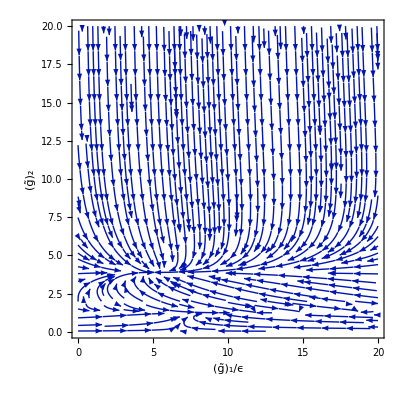

main_flow.pdf

```mathematica
range=20;
xfg=StreamPlot[{-beta1[y1,g2,4,1],-beta2[y1,g2,4,1]},{y1,0,range},{g2,0,range},StreamPoints->{Automatic,Scaled[0.005]},PlotRange-> {{0,range},{0,range}},FrameTicks->{{All,None},{All,None}},FrameTicksStyle-> Directive[FontSize-> 20,FontFamily->"Latin Modern Roman",FontColor->Black],BoundaryStyle->None,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{Style["(g̃)_1/ϵ",FontFamily->"Times",FontSize->20,FontColor->Black],Style["(g̃)_2",FontFamily->"Times",FontSize->20,FontColor->Black]},
(*PlotLabel->Style["(a) g_((V^r)_⊥)/ℵ = 0",FontFamily->"Latin Modern Roman",FontSize->20,FontColor->Black],*)
ImagePadding->{{60,40},{70,10}}
]
Export["main_flow.pdf",xfg]
```

```mathematica
f[d_,g1_,g2_]:=1/(960 (-1+d) d (-4+g2^2)^3 π^2)g2 (46080 (-1+d) d-11520 (-1+d) d g2+64 (-120+d (661+d (-604+13 d))) g2^2-160 (-4+d) (-2+d) (5+3 d) g2^3-16 (-400+d (1083+d (-902+9 d))) g2^4-80 (-40+d (13+d (7+2 d))) g2^5+4 (-280+d (623+d (-572+19 d))) g2^6+10 (-40+d (26+d+d^2)) g2^7+d (-61+(124-13 d) d) g2^8) g1
```

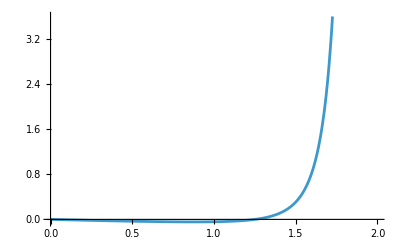

```mathematica
Plot[f[4,1,g2],{g2,0,2}]
```

## Asymmetric perturbations

## Computation for δZ_11 and δZ_13

```mathematica
LoopInt=-C1[2k-q,L,i1].G[q0,k-q,L].dband[k-q,LP].G[q0,k-q,L].C1[2k-q,L,i2]D1[w,q,i1,i2];
CT=-Subscript[δZ, 11]dband[k,LP]-Subscript[δZ, 13] dband[k,L];
CTObj1=TR[CT.dband[k,L],Contract-> False];
TrObj1=TR[LoopInt.dband[k,L],Contract-> False];
LEQ11131=LoopEvaluate[TrObj1,4,q0,q,qarr,L,LP,d,k0,k,{},{}]+LFC[CTObj1,L,LP,d,{}];
LEQ11131//TraditionalForm
CTObj2=TR[CT.dband[k,LP]];
TrObj2=TR[LoopInt.dband[k,LP]];
LEQ11132=LoopEvaluate[TrObj2,4,q0,q,qarr,L,LP,d,k0,k,{},{}]+LFC[CTObj2,L,LP,d,{}];
LEQ11132//TraditionalForm
```

LoopEvaluate(-4 dband(k,L) dband(k-q,LP) C1(2 k-q,L,i1) C1(2 k-q,L,i2) D1(w,q,i1,i2) (G(q0,k-q,L))^2,4,q0,q,qarr,L,LP,d,k0,k,{},{})+LFC(4 dband(k,L) (δZ_11 (-dband(k,LP))-δZ_13 dband(k,L)),L,LP,d,{})

LoopEvaluate(-4 dband(k,LP) dband(k-q,LP) C1(2 k-q,L,i1) C1(2 k-q,L,i2) D1(w,q,i1,i2) (G(q0,k-q,L))^2,4,q0,q,qarr,L,LP,d,k0,k,{},{})+LFC(4 dband(k,LP) (δZ_11 (-dband(k,LP))-δZ_13 dband(k,L)),L,LP,d,{})

```mathematica
SOL1113=Collect2[Solve[LEQ11131==0&&LEQ11132==0,{Subscript[δZ, 11],Subscript[δZ, 13]}],q,Factoring-> FullSimplify];
SOL1113//TraditionalForm
FullSimplify[N[Collect2[SOL1113/.{d-> 4},q,Factoring-> FullSimplify]]]
```

{}

{}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

Solve::svars: Equations may not give solutions for all "solve" variables.

## Corrections necessary below this line

## Computation for δZ_12 , δZ_14 and δZ_15

```mathematica
LoopInt=2C1[p+2q,L,i].G[w,p+q,L].C1[p+2q,L,i].G[w,q,L].dband[q,LP].G[w,q,L];
TrObj=TR[LoopInt];
LE=LoopEvaluate[TrObj,4,w,q,qarr,L,LP,p0,p,{}];
LE//TraditionalForm
CTObj=-Subscript[δZ, 15]LFC[SPd[p,p](MTd[d,i,i]SPd[p,p]-FVd[d,p,i]FVd[d,p,i]),L,LP];
LEQ15=LE+CTObj;
LEQ15//TraditionalForm
```

LoopEvaluate(8 dband(q,LP) (G(w,q,L))^2 (C1(p+2 q,L,i))^2 G(w,p+q,L),4,w,q,qarr,L,LP,p0,p,{})

LoopEvaluate(8 dband(q,LP) (G(w,q,L))^2 (C1(p+2 q,L,i))^2 G(w,p+q,L),4,w,q,qarr,L,LP,p0,p,{})-δZ_15 LFC(SPd(p,p) (g^ii SPd(p,p)-(p^i)^2),L,LP)

```mathematica
SOL15=Collect2[Solve[LEQ15==0,Subscript[δZ, 15]],q,Factoring-> FullSimplify];
SOL15//TraditionalForm
Collect2[SOL15/.{d-> 4},q,Factoring-> FullSimplify]
```

{{δZ_15→(LoopEvaluate(8 dband(q,LP) (G(w,q,L))^2 (C1(p+2 q,L,i))^2 G(w,p+q,L),4,w,q,qarr,L,LP,p0,p,{}))/(LFC(SPd(p,p) (g^ii SPd(p,p)-(p^i)^2),L,LP))}}

{{δZ_15→LoopEvaluate[8 C1[p+2 q,L,i]^2 dband[q,LP] G[w,q,L]^2 G[w,p+q,L],4,w,q,qarr,L,LP,p0,p,{}]/LFC[SPd[p,p] (-Pair[LorentzIndex[i],Momentum[p]]^2+Pair[LorentzIndex[i],LorentzIndex[i]] SPd[p,p]),L,LP]}}

```mathematica
LoopInt=2(C1[2q,L,i]).G[w+z,q,L].(C1[2q,L,i]).G[w,q,L].dband[q,LP].G[w,q,L];
TrObj=TR[LoopInt];
LE=LoopEvaluate[TrObj,2,w,q,qarr,L,LP,z,p,{}];
LE//TraditionalForm
CTObj=-d Subscript[δZ, 14] z^2;
LEQ14=LE+CTObj;
LEQ14//TraditionalForm
```

LoopEvaluate(8 dband(q,LP) (C1(2 q,L,i))^2 (G(w,q,L))^2 G(w+z,q,L),2,w,q,qarr,L,LP,z,p,{})

LoopEvaluate(8 dband(q,LP) (C1(2 q,L,i))^2 (G(w,q,L))^2 G(w+z,q,L),2,w,q,qarr,L,LP,z,p,{})-d δZ_14 z^2

```mathematica
SOL14=Collect2[Solve[LEQ14==0,Subscript[δZ, 14]],q,Factoring-> FullSimplify];
SOL14//TraditionalForm
Collect2[SOL/.{d-> 4},q,Factoring-> FullSimplify]
```

{{δZ_14→(LoopEvaluate(8 dband(q,LP) (C1(2 q,L,i))^2 (G(w,q,L))^2 G(w+z,q,L),2,w,q,qarr,L,LP,z,p,{}))/(d z^2)}}

SOL

```mathematica
SOL12={Subscript[δZ, 12]:>0}
```

{δZ_12:>0}

## Computation for δZ_21 and δZ_23

```mathematica
LoopInt=-C1[2p-q,L,i1].G[w,p-q,L].C1[2p-q,L,i4]D1[w,q,i1,i2]CubeAniso[q,qarr,t,u,i2,i3]D1[w,q,i3,i4];
CT=-Subscript[δZ, 21]dband[p,LP]-Subscript[δZ, 23] dband[p,L];
CTObj1=TR[CT.dband[p,L]];
TrObj1=TR[LoopInt.dband[p,L]];
LEQ21231=LoopEvaluate[TrObj1,4,w,q,qarr,L,LP,p0,p,{t,u}]+LFC[CTObj1,L,LP];
LEQ21231//TraditionalForm
CTObj2=TR[CT.dband[p,LP]];
TrObj2=TR[LoopInt.dband[p,LP]];
LEQ21232=LoopEvaluate[TrObj2,4,w,q,qarr,L,LP,p0,p,{t,u}]+LFC[CTObj2,L,LP];
LEQ21232//TraditionalForm
```

LoopEvaluate(-4 dband(p,L) C1(2 p-q,L,i1) C1(2 p-q,L,i4) D1(w,q,i1,i2) D1(w,q,i3,i4) G(w,p-q,L) CubeAniso(q,qarr,t,u,i2,i3),4,w,q,qarr,L,LP,p0,p,{t,u})+LFC(4 dband(p,L) (δZ_21 (-dband(p,LP))-δZ_23 dband(p,L)),L,LP)

LoopEvaluate(-4 dband(p,LP) C1(2 p-q,L,i1) C1(2 p-q,L,i4) D1(w,q,i1,i2) D1(w,q,i3,i4) G(w,p-q,L) CubeAniso(q,qarr,t,u,i2,i3),4,w,q,qarr,L,LP,p0,p,{t,u})+LFC(4 dband(p,LP) (δZ_21 (-dband(p,LP))-δZ_23 dband(p,L)),L,LP)

```mathematica
LEQT21231=Collect2[Cancel[Collect2[LFC[LEQ21231//.{u-> t,Pair[LorentzIndex[t_,d],Momentum[p,d]]^4:> Sum[Subscript[p, t]^4,{t,1,d}], Pair[LorentzIndex[t_,d],LorentzIndex[t_,d]] Pair[LorentzIndex[t_,d],Momentum[p,d]]^2:> Pair[LorentzIndex[t,d],Momentum[p,d]]^2},L,LP],{p,q,Sum[Subscript[p, #]^4,{#,1,d}],Subscript[δZ, 21],Subscript[δZ, 23]},Factoring-> FullSimplify]],{p,q,Sum[Subscript[p, #]^4,{#,1,d}],Subscript[δZ, 21],Subscript[δZ, 23]},Factoring-> FullSimplify]
LEQP21231=Coefficient[LEQT21231,p,4]
```

LFC[LFC[4 dband[p,L] (-dband[p,LP] δZ_21-dband[p,L] δZ_23),L,LP]+LoopEvaluate[-4 C1[2 p-q,L,i1] C1[2 p-q,L,i4] CubeAniso[q,qarr,t,t,i2,i3] D1[w,q,i1,i2] D1[w,q,i3,i4] dband[p,L] G[w,p-q,L],4,w,q,qarr,L,LP,p0,p,{t,t}],L,LP]

0

Sum::vloc: The variable #1 cannot be localized so that it can be assigned to numerical values.

```mathematica
LEQT21232=Collect2[Cancel[Collect2[LFC[LEQ21232//.{u-> t,Pair[LorentzIndex[t_,d],Momentum[p,d]]^4:> Sum[Subscript[p, t]^4,{t,1,d}], Pair[LorentzIndex[t_,d],LorentzIndex[t_,d]] Pair[LorentzIndex[t_,d],Momentum[p,d]]^2:> Pair[LorentzIndex[t,d],Momentum[p,d]]^2},L,LP],{p,q,Sum[Subscript[p, #]^4,{#,1,d}],Subscript[δZ, 21],Subscript[δZ, 23]},Factoring-> FullSimplify]],{p,q,Sum[Subscript[p, #]^4,{#,1,d}],Subscript[δZ, 21],Subscript[δZ, 23]},Factoring-> FullSimplify]
LEQP21232=Coefficient[LEQT21232,p,4]
```

LFC[LFC[4 dband[p,LP] (-dband[p,LP] δZ_21-dband[p,L] δZ_23),L,LP]+LoopEvaluate[-4 C1[2 p-q,L,i1] C1[2 p-q,L,i4] CubeAniso[q,qarr,t,t,i2,i3] D1[w,q,i1,i2] D1[w,q,i3,i4] dband[p,LP] G[w,p-q,L],4,w,q,qarr,L,LP,p0,p,{t,t}],L,LP]

0

Sum::vloc: The variable #1 cannot be localized so that it can be assigned to numerical values.

General::stop: Further output of Sum::vloc will be suppressed during this calculation.

Sum::vloc: The variable #1 cannot be localized so that it can be assigned to numerical values.

```mathematica
SOL2123=Collect2[Solve[LEQP21231==0&&LEQP21232==0,{Subscript[δZ, 21],Subscript[δZ, 23]}],q,Factoring-> FullSimplify];
SOL2123//TraditionalForm
FullSimplify[N[Collect2[SOL2123/.{d-> 4},q,Factoring-> FullSimplify]]]
```

{{}}

{{}}

```mathematica
Subscript[δZ, 21]
```

δZ_21

```mathematica
Flatten[Join[SOL1113,SOL12,SOL14,SOL15,SOL2123]]
```

{δZ_12:>0,δZ_14→LoopEvaluate[8 C1[2 q,L,i]^2 dband[q,LP] G[w,q,L]^2 G[w+z,q,L],2,w,q,qarr,L,LP,z,p,{}]/(d z^2),δZ_15→LoopEvaluate[8 C1[p+2 q,L,i]^2 dband[q,LP] G[w,q,L]^2 G[w,p+q,L],4,w,q,qarr,L,LP,p0,p,{}]/LFC[SPd[p,p] (-Pair[LorentzIndex[i,d],Momentum[p,d]]^2+Pair[LorentzIndex[i,d],LorentzIndex[i,d]] SPd[p,p]),L,LP]}

## Anomalous mixing matrix

```mathematica
ZMP={{Subscript[δZ, 11],Subscript[δZ, 12],Subscript[δZ, 13],Subscript[δZ, 14],Subscript[δZ, 15]},{Subscript[δZ, 21],Subscript[δZ, 22],Subscript[δZ, 23],Subscript[δZ, 24],Subscript[δZ, 25]},{Subscript[δZ, 31],Subscript[δZ, 32],Subscript[δZ, 33],Subscript[δZ, 34],Subscript[δZ, 35]},{Subscript[δZ, 41],Subscript[δZ, 42],Subscript[δZ, 43],Subscript[δZ, 44],Subscript[δZ, 45]},{Subscript[δZ, 51],Subscript[δZ, 52],Subscript[δZ, 53],Subscript[δZ, 54],Subscript[δZ, 55]}}/.Flatten[Join[SOL1113,SOL12,SOL14,SOL15,SOL2123]];
ZM=FullSimplify[IdentityMatrix[5]+ZMP/.{Subscript[δZ, x_]-> 0}];
ZM//MatrixForm
ZLM=FullSimplify[Collect2[Eigenvalues[ZM],q,FullSimplify]/.{1/q^4-> 1/(8 π^2 ϵ)}]
```

(1 | 0 | 0 | LoopEvaluate[8 C1[2 q,L,i]^2 dband[q,LP] G[w,q,L]^2 G[w+z,q,L],2,w,q,qarr,L,LP,z,p,{}]/(d z^2) | LoopEvaluate[8 C1[p+2 q,L,i]^2 dband[q,LP] G[w,q,L]^2 G[w,p+q,L],4,w,q,qarr,L,LP,p0,p,{}]/LFC[SPd[p,p] (-Pair[LorentzIndex[i,d],Momentum[p,d]]^2+Pair[LorentzIndex[i,d],LorentzIndex[i,d]] SPd[p,p]),L,LP]
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

{1,1,1,1,1}

```mathematica
ZLMP[g1_,g2_]:=FullSimplify[ZLM//.{e^2-> g1/m,m-> 1/(g2 √v)}]
```

```mathematica
ZLMP[g1,g2]
```

{1,1,1,1,1}

```mathematica
2+{1,1,2}
```

{3,3,4}

```mathematica
{3,3,4}{C1,C2,C3}
```

{3 C1,3 C2,4 C3}

```mathematica
AnomBeta[Z_,C_,RegDim_,ϵ_,g1_,g2_]:=Module[{beta1,beta2},beta1=-ϵ;beta2=0;FullSimplify[-(RegDim+beta1 D[Z,g1]+beta2 D[Z,g2])C]]
```

```mathematica
AnomBeta[ZLMP[g1,g2],{C1,C2,C3,C4,C5},0,ϵ,g1,g2]/.{g1-> 4.3474 ϵ,g2-> 2.42705,d-> 4}
```

{0,0,0,0,0}